```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
WorldPoints = {a,b,c,d,aPrime,bPrime,cPrime,dPrime,d2Prime};
Oc={0,0,0,1};
zeta1 = -1;
zeta2=-1;
alpha=45;
beta = 0;
Oc2={6,0,0,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{2,0,0,0},{0,2,0,0},{0,0,1,0},{0,0,0,1}};
AK={{2,0,0},{0,2,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-2,0,0,0},{0,-2,0,0},{0,0,-1,0},{0,0,1,0}}

OC2 = {6,0,0,1}

M of C2=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

M2 of C1 =(0.707107 | 0. | -0.707107 | -4.24264
0. | 1. | 0. | 0.
0.707107 | 0. | 0.707107 | -4.24264
0. | 0. | 0. | 1.)

ProjectionMtxCamera1(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-1.41421 | 0. | 1.41421 | 8.48528
0. | -2. | 0. | 0.
-0.707107 | 0. | -0.707107 | 4.24264
0.707107 | 0. | 0.707107 | -4.24264)

CameraProjectedPointsK1 = (-3 | -3 | 4 | -4
-5 | -3 | 4 | -4
-5 | -5 | 4 | -4
-3 | -5 | 4 | -4
-3 | -3 | 6 | -6
-5 | -3 | 6 | -6
-5 | -5 | 6 | -6
-3 | -5 | 6 | -6
-8 | -8 | 6 | -6)

CameraProjectedPointsK2 = (-1.41421 | -6. | 4.94975 | -4.94975
-4.24264 | -6. | 3.53553 | -3.53553
-4.24264 | -10. | 3.53553 | -3.53553
-1.41421 | -10. | 4.94975 | -4.94975
-4.24264 | -6. | 6.36396 | -6.36396
-7.07107 | -6. | 4.94975 | -4.94975
-7.07107 | -10. | 4.94975 | -4.94975
-4.24264 | -10. | 6.36396 | -6.36396
-11.3137 | -16. | 2.82843 | -2.82843)

homogene CameraProjectedPointsK1 = (3/4 | 3/4 | -1 | 1
5/4 | 3/4 | -1 | 1
5/4 | 5/4 | -1 | 1
3/4 | 5/4 | -1 | 1
1/2 | 1/2 | -1 | 1
5/6 | 1/2 | -1 | 1
5/6 | 5/6 | -1 | 1
1/2 | 5/6 | -1 | 1
4/3 | 4/3 | -1 | 1)

homogene CameraProjectedPointsK2 = (0.285714 | 1.21218 | -1. | 1.
1.2 | 1.69706 | -1. | 1.
1.2 | 2.82843 | -1. | 1.
0.285714 | 2.02031 | -1. | 1.
0.666667 | 0.942809 | -1. | 1.
1.42857 | 1.21218 | -1. | 1.
1.42857 | 2.02031 | -1. | 1.
0.666667 | 1.57135 | -1. | 1.
4. | 5.65685 | -1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

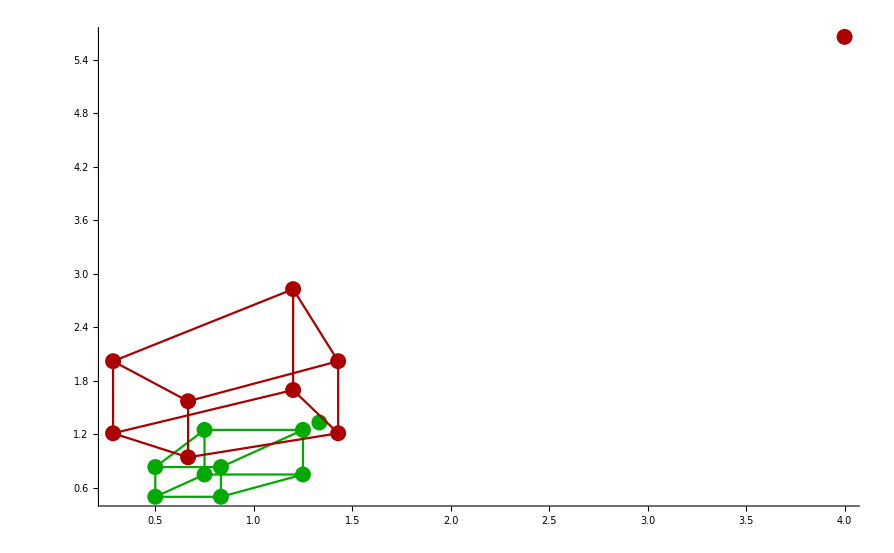

ImagePlaneC1Points = (3/4 | 3/4 | 1
5/4 | 3/4 | 1
5/4 | 5/4 | 1
3/4 | 5/4 | 1
1/2 | 1/2 | 1
5/6 | 1/2 | 1
5/6 | 5/6 | 1
1/2 | 5/6 | 1
4/3 | 4/3 | 1)

ImagePlaneC2Points = (0.285714 | 1.21218 | 1.
1.2 | 1.69706 | 1.
1.2 | 2.82843 | 1.
0.285714 | 2.02031 | 1.
0.666667 | 0.942809 | 1.
1.42857 | 1.21218 | 1.
1.42857 | 2.02031 | 1.
0.666667 | 1.57135 | 1.
4. | 5.65685 | 1.)

CoefficientMtx = (0.214286 | 0.214286 | 0.285714 | 0.909137 | 0.909137 | 1.21218 | 0.75 | 0.75 | 1.
1.5 | 0.9 | 1.2 | 2.12132 | 1.27279 | 1.69706 | 1.25 | 0.75 | 1.
1.5 | 1.5 | 1.2 | 3.53553 | 3.53553 | 2.82843 | 1.25 | 1.25 | 1.
0.214286 | 0.357143 | 0.285714 | 1.51523 | 2.52538 | 2.02031 | 0.75 | 1.25 | 1.
0.333333 | 0.333333 | 0.666667 | 0.471405 | 0.471405 | 0.942809 | 0.5 | 0.5 | 1.
1.19048 | 0.714286 | 1.42857 | 1.01015 | 0.606092 | 1.21218 | 0.833333 | 0.5 | 1.
1.19048 | 1.19048 | 1.42857 | 1.68359 | 1.68359 | 2.02031 | 0.833333 | 0.833333 | 1.
0.333333 | 0.555556 | 0.666667 | 0.785674 | 1.30946 | 1.57135 | 0.5 | 0.833333 | 1.
5.33333 | 5.33333 | 4. | 7.54247 | 7.54247 | 5.65685 | 1.33333 | 1.33333 | 1.)

MatrixRank[CoefficientMtx]8

ns ={{1.82985×10^-16,0.377964,-1.61649×10^-15,-2.85833×10^-15,1.89634×10^-15,-0.534522,4.81564×10^-15,0.755929,-1.73058×10^-16}}

F = (1.82985×10^-16 | 0.377964 | -1.61649×10^-15
-2.85833×10^-15 | 1.89634×10^-15 | -0.534522
4.81564×10^-15 | 0.755929 | -1.73058×10^-16)

lC1 = {{0.283473,-0.534522,0.566947},{0.283473,-0.534522,0.566947},{0.472456,-0.534522,0.944911},{0.472456,-0.534522,0.944911},{0.188982,-0.534522,0.377964},{0.188982,-0.534522,0.377964},{0.31497,-0.534522,0.629941},{0.31497,-0.534522,0.629941},{0.503953,-0.534522,1.00791}}

lPrimeC1 = {{1.4031×10^-15,0.863919,-0.647939},{1.84472×10^-16,1.20949,-0.907115},{-3.04936×10^-15,1.20949,-1.51186},{-9.06781×10^-16,0.863919,-1.0799},{2.24277×10^-15,1.00791,-0.503953},{1.61223×10^-15,1.29588,-0.647939},{-6.97655×10^-16,1.29588,-1.0799},{4.46195×10^-16,1.00791,-0.839921},{-1.06216×10^-14,2.26779,-3.02372}}

e = {1.,-5.10703×10^-15,-5.34534×10^-15}

e' = {0.894427,-2.66297×10^-15,-0.447214}

EpipoleLines = (0.5 | -0.942809 | 1.
0.5 | -0.942809 | 1.
0.5 | -0.565685 | 1.
0.5 | -0.565685 | 1.
0.5 | -1.41421 | 1.
0.5 | -1.41421 | 1.
0.5 | -0.848528 | 1.
0.5 | -0.848528 | 1.
0.5 | -0.53033 | 1.)

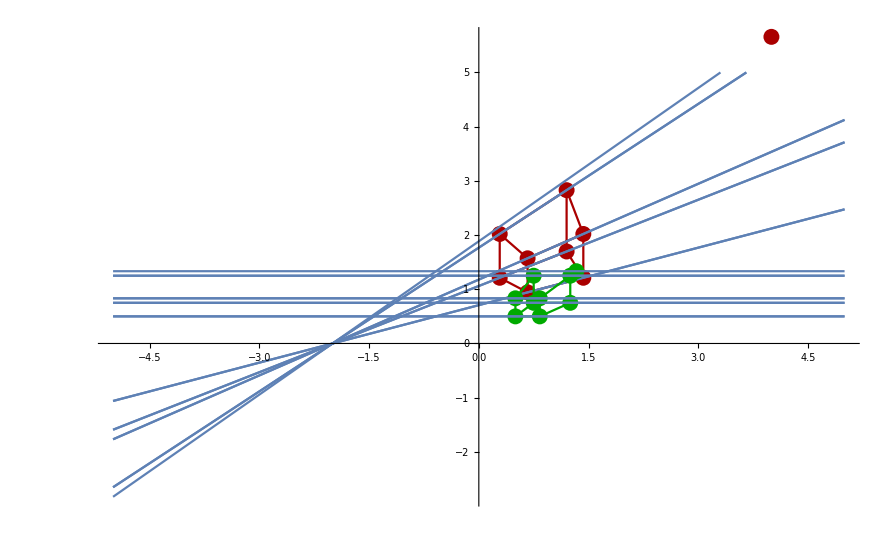

Begin Computing essential Matrix___________________________________________________

EMtx = (3.65969×10^-16 | 0.755929 | 3.23297×10^-15
-5.71666×10^-15 | 3.79268×10^-15 | 1.06904
-4.81564×10^-15 | -0.755929 | -1.73058×10^-16)

U of E = {{-0.707107,-4.09719×10^-15,0.707107},{-7.85046×10^-15,1.,-2.0773×10^-15},{0.707107,6.88338×10^-15,0.707107}}

Sigma of E = {{1.06904,0.,0.},{0.,1.06904,0.},{0.,0.,0.}}

V of E = {{-3.33067×10^-15,-5.375×10^-15,-1.},{-1.,-1.00711×10^-14,3.33067×10^-15},{-1.00711×10^-14,1.,-5.33631×10^-15}}

S1 = (0. | 0.707107 | 1.97014×10^-15
-0.707107 | 0. | 0.707107
-1.97014×10^-15 | -0.707107 | 0.)

S2 = (0. | -0.707107 | -1.97014×10^-15
0.707107 | 0. | -0.707107
1.97014×10^-15 | 0.707107 | 0.)

R1 = (0.707107 | -5.37931×10^-15 | 0.707107
-5.40797×10^-15 | -1. | -2.22066×10^-15
0.707107 | -2.11716×10^-15 | -0.707107)

R2 = (0.707107 | 6.6903×10^-16 | -0.707107
1.25337×10^-15 | 1. | 2.22066×10^-15
0.707107 | -2.59311×10^-15 | 0.707107)

Test R1 is rotation ={{1.,1.07166×10^-16,0.},{1.07166×10^-16,1.,-8.60254×10^-17},{0.,-8.60254×10^-17,1.}}

Test R2 is rotation ={{1.,-1.07166×10^-16,0.},{-1.07166×10^-16,1.,-8.60254×10^-17},{0.,-8.60254×10^-17,1.}}

Check if t of S1, S2 is equal = {{{0.707107,-1.9984×10^-15,0.707107}},{{0.707107,-1.9984×10^-15,0.707107}}}

t = {0.707107,-1.9984×10^-15,0.707107}

P21  = (0.707107 | 6.6903×10^-16 | -0.707107 | -0.707107
1.25337×10^-15 | 1. | 2.22066×10^-15 | 1.9984×10^-15
0.707107 | -2.59311×10^-15 | 0.707107 | -0.707107)

P22  = (0.707107 | -5.37931×10^-15 | 0.707107 | -0.707107
-5.40797×10^-15 | -1. | -2.22066×10^-15 | 1.9984×10^-15
0.707107 | -2.11716×10^-15 | -0.707107 | -0.707107)

P23  = (0.707107 | 6.6903×10^-16 | -0.707107 | 0.707107
1.25337×10^-15 | 1. | 2.22066×10^-15 | -1.9984×10^-15
0.707107 | -2.59311×10^-15 | 0.707107 | 0.707107)

P24  = (0.707107 | -5.37931×10^-15 | 0.707107 | 0.707107
-5.40797×10^-15 | -1. | -2.22066×10^-15 | -1.9984×10^-15
0.707107 | -2.11716×10^-15 | -0.707107 | 0.707107)

End Computing essential Matrix___________________________________________________

PList = {{{0.707107,6.6903×10^-16,-0.707107,-0.707107},{1.25337×10^-15,1.,2.22066×10^-15,1.9984×10^-15},{0.707107,-2.59311×10^-15,0.707107,-0.707107}},{{0.707107,-5.37931×10^-15,0.707107,-0.707107},{-5.40797×10^-15,-1.,-2.22066×10^-15,1.9984×10^-15},{0.707107,-2.11716×10^-15,-0.707107,-0.707107}},{{0.707107,6.6903×10^-16,-0.707107,0.707107},{1.25337×10^-15,1.,2.22066×10^-15,-1.9984×10^-15},{0.707107,-2.59311×10^-15,0.707107,0.707107}},{{0.707107,-5.37931×10^-15,0.707107,0.707107},{-5.40797×10^-15,-1.,-2.22066×10^-15,-1.9984×10^-15},{0.707107,-2.11716×10^-15,-0.707107,0.707107}}}

Length PList = 4

End Reconstruction of Rotation and Translation________________________________________________

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{0.5,0.5,-0.666667},{0.833333,0.5,-0.666667},{0.833333,0.833333,-0.666667},{0.5,0.833333,-0.666667},{0.5,0.5,-1.},{0.833333,0.5,-1.},{0.833333,0.833333,-1.},{0.5,0.833333,-1.},{1.33333,1.33333,-1.}}

ScaleValue = 6.

RForOk2 = {{0.707107,1.25337×10^-15,0.707107},{6.6903×10^-16,1.,-2.59311×10^-15},{-0.707107,2.22066×10^-15,0.707107}}

tForOK2 = {-0.707107,1.9984×10^-15,-0.707107}

t = {1.,-3.35893×10^-15,5.32907×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

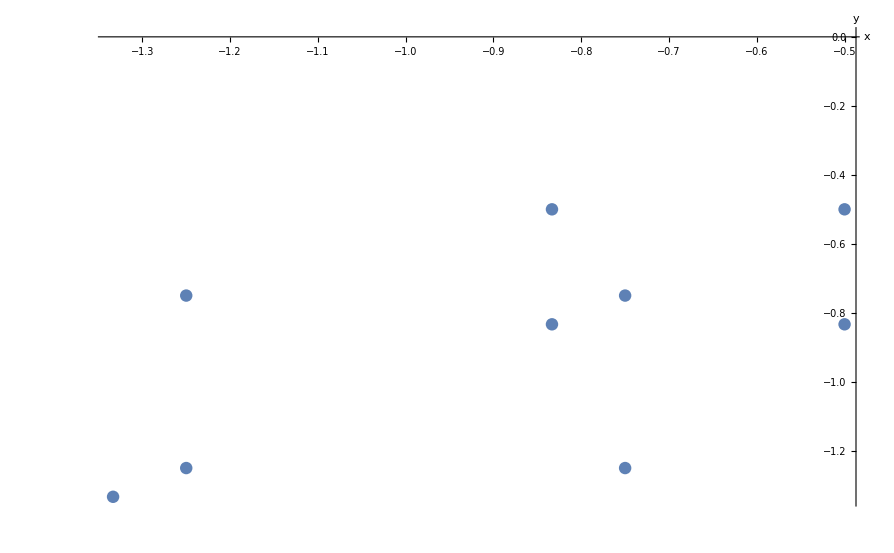

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-3.51328×10^13,-3.51328×10^13,4.68438×10^13},{1.25,0.75,-1.},{1.25,1.25,-1.},{-3.15036×10^13,-5.2506×10^13,4.20048×10^13},{-3.07239×10^13,-3.07239×10^13,6.14478×10^13},{1.25,0.75,-1.5},{1.25,1.25,-1.5},{-2.77733×10^13,-4.62888×10^13,5.55466×10^13},{0.8,0.8,-0.6}}

ScaleValue = -8.53902×10^-14

RForOk2 = {{0.707107,-5.40797×10^-15,0.707107},{-5.37931×10^-15,-1.,-2.11716×10^-15},{0.707107,-2.22066×10^-15,-0.707107}}

tForOK2 = {-0.707107,1.9984×10^-15,-0.707107}

t = {1.,-3.3024×10^-15,5.32907×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
-1.06738×10^-13 | -6.40427×10^-14 | 8.53902×10^-14
-1.06738×10^-13 | -1.06738×10^-13 | 8.53902×10^-14
2.6901 | 4.4835 | -3.5868
2.62352 | 2.62352 | -5.24704
-1.06738×10^-13 | -6.40427×10^-14 | 1.28085×10^-13
-1.06738×10^-13 | -1.06738×10^-13 | 1.28085×10^-13
2.37157 | 3.95261 | -4.74314
-6.83122×10^-14 | -6.83122×10^-14 | 5.12341×10^-14)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-0.5,-0.5,0.666667},{-0.833333,-0.5,0.666667},{-0.833333,-0.833333,0.666667},{-0.5,-0.833333,0.666667},{-0.5,-0.5,1.},{-0.833333,-0.5,1.},{-0.833333,-0.833333,1.},{-0.5,-0.833333,1.},{-1.33333,-1.33333,1.}}

ScaleValue = -6.

RForOk2 = {{0.707107,1.25337×10^-15,0.707107},{6.6903×10^-16,1.,-2.59311×10^-15},{-0.707107,2.22066×10^-15,0.707107}}

tForOK2 = {0.707107,-1.9984×10^-15,0.707107}

t = {-1.,3.35893×10^-15,-5.32907×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-2 | 0 | 0
0 | -2 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{3.51328×10^13,3.51328×10^13,-4.68438×10^13},{-1.25,-0.75,1.},{-1.25,-1.25,1.},{3.15036×10^13,5.2506×10^13,-4.20048×10^13},{3.07239×10^13,3.07239×10^13,-6.14478×10^13},{-1.25,-0.75,1.5},{-1.25,-1.25,1.5},{2.77733×10^13,4.62888×10^13,-5.55466×10^13},{-0.8,-0.8,0.6}}

ScaleValue = 8.53902×10^-14

RForOk2 = {{0.707107,-5.40797×10^-15,0.707107},{-5.37931×10^-15,-1.,-2.11716×10^-15},{0.707107,-2.22066×10^-15,-0.707107}}

tForOK2 = {0.707107,-1.9984×10^-15,0.707107}

t = {-1.,3.3024×10^-15,-5.32907×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
-1.06738×10^-13 | -6.40427×10^-14 | 8.53902×10^-14
-1.06738×10^-13 | -1.06738×10^-13 | 8.53902×10^-14
2.6901 | 4.4835 | -3.5868
2.62352 | 2.62352 | -5.24704
-1.06738×10^-13 | -6.40427×10^-14 | 1.28085×10^-13
-1.06738×10^-13 | -1.06738×10^-13 | 1.28085×10^-13
2.37157 | 3.95261 | -4.74314
-6.83122×10^-14 | -6.83122×10^-14 | 5.12341×10^-14)

-Graphics3D-

-Graphics-

Start Rectification_________________________________________________________________________

z = {1.,1.,0.}

wPrime = {0.377964,-9.61992×10^-16,0.755929}

w = {5.34534×10^-15,-5.34534×10^-15,1.}

wPrime = {0.5,-1.2726×10^-15,1.}

w = {5.34534×10^-15,-5.34534×10^-15,1.}

HpPrime = (1. | 0. | 0.
0. | 1. | 0.
0.5 | -1.2726×10^-15 | 1.)

Hp = (1. | 0. | 0.
0. | 1. | 0.
5.34534×10^-15 | -5.34534×10^-15 | 1.)

ePrime inf = {0.894427,-2.66297×10^-15,-2.60902×10^-15}

e inf = {1.,-5.10703×10^-15,7.88861×10^-31}

HrPrime = (0.534522 | -1.52996×10^-15 | 0.
1.52996×10^-15 | 0.534522 | 0.
0. | 0. | 1.)

Hr = (0.755929 | -4.81564×10^-15 | 0.
4.81564×10^-15 | 0.755929 | -1.73058×10^-16
0. | 0. | 1.)

ePrimeHorizontal = {0.478091,-5.49807×10^-17,-2.60902×10^-15}

eHorizontal = {0.755929,9.55092×10^-16,7.88861×10^-31}

RecPointsC2 =(0.133631 | 0.566947 | 1.
0.400892 | 0.566947 | 1.
0.400892 | 0.944911 | 1.
0.133631 | 0.944911 | 1.
0.267261 | 0.377964 | 1.
0.445435 | 0.377964 | 1.
0.445435 | 0.629941 | 1.
0.267261 | 0.629941 | 1.)

RecPointsC1 =(0.566947 | 0.566947 | 1.
0.944911 | 0.566947 | 1.
0.944911 | 0.944911 | 1.
0.566947 | 0.944911 | 1.
0.377964 | 0.377964 | 1.
0.629941 | 0.377964 | 1.
0.629941 | 0.629941 | 1.
0.377964 | 0.629941 | 1.)

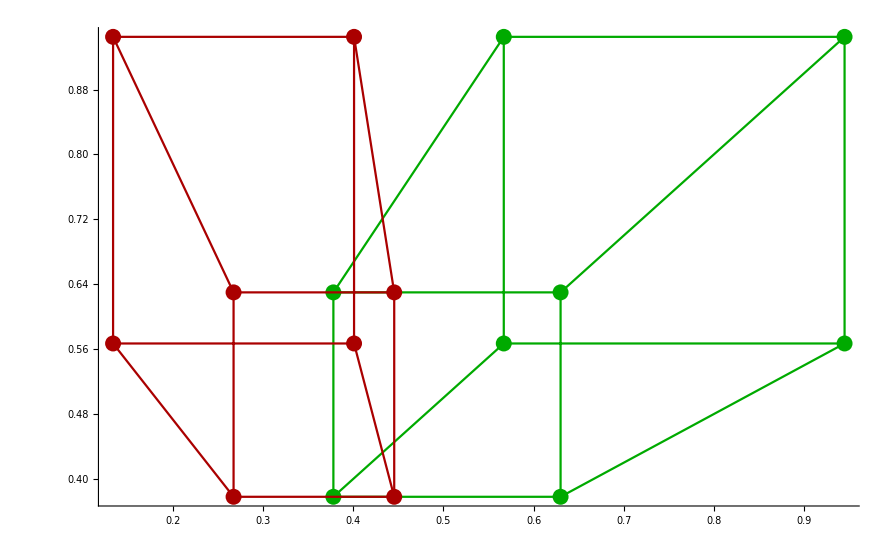

End Rectification___________________________________________________________________________

```mathematica
StartComputation[];
```